```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 2 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
Clear[q1]
q1 = { x[t] , y[t], z[t] } 
q1[[2]]
```

{x[t],y[t],z[t]}

y[t]

```mathematica
D[q1, t]
```

{x'[t],y'[t],z'[t]}

```mathematica
D[q1, t] . D[q1, t]
```

x'[t]^2+y'[t]^2+z'[t]^2

```mathematica
Clear[q2]
q2 = { r[t] , θ[t], ϕ[t] }
```

{r[t],θ[t],ϕ[t]}

```mathematica
r2 = { r[t] Cos[ϕ[t]] Sin[θ[t]] , r[t] Sin[ϕ[t]] Sin[θ[t]], r[t] Cos[θ[t]] }
```

{Cos[ϕ[t]] r[t] Sin[θ[t]],r[t] Sin[θ[t]] Sin[ϕ[t]],Cos[θ[t]] r[t]}

```mathematica
D[r2, t]
```

{Cos[ϕ[t]] Sin[θ[t]] r'[t]+Cos[θ[t]] Cos[ϕ[t]] r[t] θ'[t]-r[t] Sin[θ[t]] Sin[ϕ[t]] ϕ'[t],Sin[θ[t]] Sin[ϕ[t]] r'[t]+Cos[θ[t]] r[t] Sin[ϕ[t]] θ'[t]+Cos[ϕ[t]] r[t] Sin[θ[t]] ϕ'[t],Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t]}

```mathematica
D[r2, t] . D[r2, t]
```

(Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t])^2+(Sin[θ[t]] Sin[ϕ[t]] r'[t]+Cos[θ[t]] r[t] Sin[ϕ[t]] θ'[t]+Cos[ϕ[t]] r[t] Sin[θ[t]] ϕ'[t])^2+(Cos[ϕ[t]] Sin[θ[t]] r'[t]+Cos[θ[t]] Cos[ϕ[t]] r[t] θ'[t]-r[t] Sin[θ[t]] Sin[ϕ[t]] ϕ'[t])^2

```mathematica
D[r2, t] . D[r2, t]  // Expand
```

Cos[θ[t]]^2 r'[t]^2+Cos[ϕ[t]]^2 Sin[θ[t]]^2 r'[t]^2+Sin[θ[t]]^2 Sin[ϕ[t]]^2 r'[t]^2-2 Cos[θ[t]] r[t] Sin[θ[t]] r'[t] θ'[t]+2 Cos[θ[t]] Cos[ϕ[t]]^2 r[t] Sin[θ[t]] r'[t] θ'[t]+2 Cos[θ[t]] r[t] Sin[θ[t]] Sin[ϕ[t]]^2 r'[t] θ'[t]+Cos[θ[t]]^2 Cos[ϕ[t]]^2 r[t]^2 θ'[t]^2+r[t]^2 Sin[θ[t]]^2 θ'[t]^2+Cos[θ[t]]^2 r[t]^2 Sin[ϕ[t]]^2 θ'[t]^2+Cos[ϕ[t]]^2 r[t]^2 Sin[θ[t]]^2 ϕ'[t]^2+r[t]^2 Sin[θ[t]]^2 Sin[ϕ[t]]^2 ϕ'[t]^2

```mathematica
D[r2, t] . D[r2, t]  // Expand // Simplify
```

r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)

```mathematica
Clear[q]
q = Union[q1,q2]
```

{r[t],x[t],y[t],z[t],θ[t],ϕ[t]}

```mathematica
( D[r2, t] . D[r2, t] /. { r[t]-> 1, r'[t]-> 0 } )  // Expand // Simplify
```

θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2

```mathematica
Clear[T]
T = 1/2( M + 2 m ) ( D[q1, t] . D[q1, t]  ) + 1/2(2 m ) ( D[r2, t] . D[r2, t]  // Expand // Simplify  ) + 1/2(1/12 M L^2) (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)
```

1/2 (2 m+M) (x'[t]^2+y'[t]^2+z'[t]^2)+1/24 L^2 M (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+m (r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2))

```mathematica
Clear[V]
V = 2 ( 1/2 K ( r[t] - r0 )^2)
```

K (-r0+r[t])^2

```mathematica
Clear[ℒ]
ℒ = T - V
```

-K (-r0+r[t])^2+1/2 (2 m+M) (x'[t]^2+y'[t]^2+z'[t]^2)+1/24 L^2 M (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+m (r'[t]^2+r[t]^2 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2))

```mathematica
D[ D[ ℒ , D[q[[3]], t] ] ,t ] -D[ ℒ,q[[3]] ] 
D[ D[ ℒ , D[q[[5]], t] ] ,t ] -D[ ℒ,q[[5]] ]
```

(2 m+M) y''[t]

4 m r[t] r'[t] θ'[t]-1/12 L^2 M Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2-2 m Cos[θ[t]] r[t]^2 Sin[θ[t]] ϕ'[t]^2+1/12 L^2 M θ''[t]+2 m r[t]^2 θ''[t]

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ] ,t ] -D[ ℒ,q[[i]] ]== 0 ,
{i,1,6} ]  // TableForm
```

2 K (-r0+r[t])-2 m r[t] (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+2 m r''[t]==0
(2 m+M) x''[t]==0
(2 m+M) y''[t]==0
(2 m+M) z''[t]==0
4 m r[t] r'[t] θ'[t]-1/12 L^2 M Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2-2 m Cos[θ[t]] r[t]^2 Sin[θ[t]] ϕ'[t]^2+1/12 L^2 M θ''[t]+2 m r[t]^2 θ''[t]==0
4 m r[t] Sin[θ[t]]^2 r'[t] ϕ'[t]+1/6 L^2 M Cos[θ[t]] Sin[θ[t]] θ'[t] ϕ'[t]+4 m Cos[θ[t]] r[t]^2 Sin[θ[t]] θ'[t] ϕ'[t]+1/12 L^2 M Sin[θ[t]]^2 ϕ''[t]+2 m r[t]^2 Sin[θ[t]]^2 ϕ''[t]==0

```mathematica
Clear[eqs]
eqs = EulerEquations[ ℒ , q, t ] ;
eqs // TableForm
```

2 K (r0-r[t])+2 m r[t] (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)-2 m r''[t]==0
-(2 m+M) x''[t]==0
-(2 m+M) y''[t]==0
-(2 m+M) z''[t]==0
-4 m r[t] r'[t] θ'[t]+1/24 L^2 M (Sin[2 θ[t]] ϕ'[t]^2-2 θ''[t])+m r[t]^2 (Sin[2 θ[t]] ϕ'[t]^2-2 θ''[t])==0
-1/12 Sin[θ[t]] (48 m r[t] Sin[θ[t]] r'[t] ϕ'[t]+L^2 M (2 Cos[θ[t]] θ'[t] ϕ'[t]+Sin[θ[t]] ϕ''[t])+24 m r[t]^2 (2 Cos[θ[t]] θ'[t] ϕ'[t]+Sin[θ[t]] ϕ''[t]))==0

```mathematica
Clear[com]
com = FirstIntegrals[ ℒ , q , t ] ;
com // TableForm
```

FirstIntegral[x]→-(2 m+M) x'[t]
FirstIntegral[y]→-(2 m+M) y'[t]
FirstIntegral[z]→-(2 m+M) z'[t]
FirstIntegral[ϕ]→-1/12 (L^2 M+24 m r[t]^2) Sin[θ[t]]^2 ϕ'[t]
FirstIntegral[t]→K r0^2-2 K r0 r[t]+m r'[t]^2+m x'[t]^2+1/2 M x'[t]^2+m y'[t]^2+1/2 M y'[t]^2+m z'[t]^2+1/2 M z'[t]^2+1/24 L^2 M θ'[t]^2+1/24 L^2 M Sin[θ[t]]^2 ϕ'[t]^2+r[t]^2 (K+m θ'[t]^2+m Sin[θ[t]]^2 ϕ'[t]^2)

```mathematica
Clear[ics]
ics = { 
x[0] == 1,
x'[0] == 1,
y[0] == 1 ,
y'[0] == 1,
z[0] == 1,
z'[0] == 1,
r[0] == 1,
r'[0] == 1,
θ[0] == 1,
θ'[0] == 1,
ϕ[0] == 1,
ϕ'[0] == 1
} ;
ics // TableForm
```

x[0]==1
x'[0]==1
y[0]==1
y'[0]==1
z[0]==1
z'[0]==1
r[0]==1
r'[0]==1
θ[0]==1
θ'[0]==1
ϕ[0]==1
ϕ'[0]==1

```mathematica
Clear[parameters]
parameters = { 
m-> 2 ,
M -> 10 ,
L-> 2,
K-> 2,
r0 ->  2
} ;
```

```mathematica
eqs //. parameters
```

{4 (2-r[t])+4 r[t] (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)-4 r''[t]==0,-14 x''[t]==0,-14 y''[t]==0,-14 z''[t]==0,-8 r[t] r'[t] θ'[t]+5/3 (Sin[2 θ[t]] ϕ'[t]^2-2 θ''[t])+2 r[t]^2 (Sin[2 θ[t]] ϕ'[t]^2-2 θ''[t])==0,-1/12 Sin[θ[t]] (96 r[t] Sin[θ[t]] r'[t] ϕ'[t]+40 (2 Cos[θ[t]] θ'[t] ϕ'[t]+Sin[θ[t]] ϕ''[t])+48 r[t]^2 (2 Cos[θ[t]] θ'[t] ϕ'[t]+Sin[θ[t]] ϕ''[t]))==0}

```mathematica
Clear[solution]
solution =
NDSolve[ Union[ eqs //. parameters , ics ] , q , { t,0,10 } ]
```

{{r[t]→InterpolatingFunction[…][t],x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],z[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t],ϕ[t]→InterpolatingFunction[…][t]}}

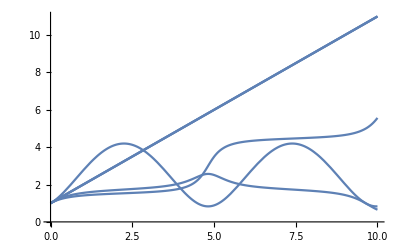

```mathematica
Plot[ q /. solution , { t, 0, 10 } ]
```

```mathematica
Exit[]
Quit[]
```